```mathematica
(*<<Neurogrid`*)
```

# ADC mismatch analysis

## Universal Code

## Plot Explorer Code

The following code was taken from: http://mathematica.stackexchange.com/questions/7142/how-to-manipulate-2d-plots
More notes about how to navigate with this feature is written at this link.

```mathematica
Attributes[PlotExplorer]={HoldFirst};
PlotExplorer[defPlot_]:=DynamicModule[{held,head,plot,range,zoomRange,defRange,defSize,defEpilog,size,pt1,pt2,spt1,dist,rect={},dragged=False,overButton=False,pushedButton=False,overHor=False,overVer=False,activeHor=False,activeVer=False,xPos=.5,yPos=.5,minDistance=0.1,sliderRatio=0.05,panFactor=10,reset,distance,slider,replot,coord=None},held=Hold@defPlot;
head=Part[held,1,0];
plot=defPlot;
{defEpilog,defRange}={Epilog,PlotRange}/.Quiet@AbsoluteOptions@plot;
defEpilog=defEpilog/.Epilog->{};
size=defSize=Rasterize[plot,"RasterSize"];
range=zoomRange=defRange;
Deploy@EventHandler[Dynamic[MouseAppearance[Show[plot,PlotRange->Dynamic@range,Epilog->{defEpilog,(*Original epilog*)(*Replot button*)EventHandler[Inset[Graphics[{Black,Dynamic@Opacity@If[overButton,If[pushedButton,.2,.1],0],Rectangle[{0,0},{1,1},RoundingRadius->Offset@5],Black,Dynamic@Opacity@If[overButton,If[pushedButton,.9,.7],0],Text["Replot",Center]},ImageSize->50,AspectRatio->1/2,BaseStyle->{FontFamily->"Helvetica"}],Scaled@{1,1},Scaled@{1,1}],{"MouseEntered":>(overButton=True),"MouseExited":>(overButton=False),"MouseDown":>(pushedButton=True),"MouseUp":>(pushedButton=False;replot@plot)}],(*Zoom rectangle*)FaceForm@{Blue,Opacity@.1},EdgeForm@{Thin,Dotted,Opacity@.5},Dynamic@rect,(*Range sliders*)Inset[slider[Dynamic@xPos,Dynamic@overHor,Dynamic@activeHor,size,True],Scaled@{.5,0},Scaled@{.5,0}],Inset[slider[Dynamic@yPos,Dynamic@overVer,Dynamic@activeVer,size,False],Scaled@{0,.5},Scaled@{0,.5}]}],(*cursor*)Which[dragged,"FrameRisingResize",CurrentValue@"AltKey",Graphics[{Antialiasing->False,Line@{{-1,0},{1,0}},Line@{{0,-1},{0,1}},Dynamic@Text[Style[coord,FontFamily->"Helvetica",8],{0,0},{-1.1,-1}]},ImageSize->160,ImagePadding->0,AspectRatio->1,PlotRange->{{-1,1},{-1,1}}*8],CurrentValue@"ControlKey"&&!overHor&&!overVer,"ZoomView",CurrentValue@"ShiftKey"&&!overHor&&!overVer,"DragGraphics",CurrentValue@"ShiftKey"&&(overHor||overVer),"LinkHand",True,Automatic]],TrackedSymbols:>{dragged,plot}],{"MouseMoved":>(coord=MousePosition@"Graphics"),"MouseClicked":>If[!overButton&&CurrentValue@"MouseClickCount"==2,reset[]],"MouseDown":>If[(!overHor||!overVer),pt1=MousePosition@"Graphics";
spt1=MousePosition@"GraphicsScaled"],"MouseDragged":>If[(!overHor&&!overVer||dragged)&&!overButton&&!pushedButton&&!activeVer&&!activeHor,dragged=True;
Which[CurrentValue@"ControlKey",dist=Last@MousePosition@"GraphicsScaled"-Last@spt1;
range=zoomRange*10^dist,(*"GraphicsScaled" is required below as "Graphics" would give jumpy results as the plot range is constantly modified.*)CurrentValue@"ShiftKey",pt2=MapThread[Rescale,{MousePosition@"GraphicsScaled",{{0,1},{0,1}},zoomRange}]-pt1;
range=zoomRange-pt2,True,pt2=MousePosition@"Graphics";
rect=If[pt2===None,{},Rectangle[pt1,pt2]]]],"MouseUp":>(If[!CurrentValue@"ShiftKey"&&!CurrentValue@"ControlKey"&&dragged&&distance[pt1,pt2,zoomRange]>minDistance,rect={};
range=Transpose@Sort@{pt1,pt2};];zoomRange=range;
dragged=False)},PassEventsDown->True,PassEventsUp->True],Initialization:>(slider[Dynamic[pos_],Dynamic[over_],Dynamic[active_],size_,hor_]:=EventHandler[Dynamic[LocatorPane[If[hor,Dynamic[{pos,.5},(pos=Clip[First@#,{0,1}];
range[[1]]=If[CurrentValue@"ShiftKey",First@zoomRange+(pos-.5)*Abs[Subtract@@First@zoomRange]*panFactor,First@zoomRange*10^((pos-.5)*2)])&],Dynamic[{.5,pos},(pos=Clip[Last@#,{0,1}];
range[[2]]=If[CurrentValue@"ShiftKey",Last@zoomRange+(pos-.5)*Abs[Subtract@@Last@zoomRange]*panFactor,Last@zoomRange*10^((pos-.5)*2)])&]],(*Locator below is required inside Graphics as LocatorPane inside Inset looses the crosshair image.*)Graphics[{Black,Opacity@If[(over||active)&&!dragged,.1,0],Rectangle[{0,0},{1,1},RoundingRadius->Offset@5],Opacity@1,Locator[Dynamic@If[hor,{pos,.5},{.5,pos}],Appearance->If[(over||active)&&!dragged,Automatic,None]]},ImagePadding->0,PlotRangePadding->0,ImageSize->If[hor,#*{1,0}+{0,20}&,#*{0,1}+{20,0}&]@size,AspectRatio->If[hor,1/sliderRatio/First@size,sliderRatio*Last@size]],Enabled->(over||active),Appearance->None,FrameMargins->0,ContentPadding->False],TrackedSymbols:>{pos,over,active,dragged}],{"MouseDown":>(active=True),"MouseUp":>(active=False),"MouseEntered":>(over=!If[hor,activeVer,activeHor]),(*The value of `active` must be public so that one slider can check whether the other is dragged,not to pop up if the other locator is moved over this slider's area.*)"MouseExited":>(over=False)},PassEventsDown->True];
replot[p_]:=Module[{temp},Switch[head,Plot,temp=ReplacePart[held,{{1,2}->{held[[1,2,1]],range[[1,1]],range[[1,2]]}}];
(*Replace plot range or insert if nonexistent*)plot=ReleaseHold@If[MemberQ[temp,PlotRange,Infinity],temp/.{_[PlotRange,_]->(PlotRange->range)},Insert[temp,PlotRange->range,{1,-1}]],DensityPlot|ContourPlot|RegionPlot|StreamPlot|StreamDensityPlot|VectorPlot|VectorDensityPlot|LineIntegralConvolutionPlot,temp=ReplacePart[held,{{1,2}->{held[[1,2,1]],range[[1,1]],range[[1,2]]},{1,3}->{held[[1,3,1]],range[[2,1]],range[[2,2]]}}];
plot=ReleaseHold@If[MemberQ[temp,PlotRange,Infinity],temp/.{_[PlotRange,_]->(PlotRange->range)},Insert[temp,PlotRange->range,{1,-1}]];,_,Null]];
reset[]:=(range=zoomRange=defRange;xPos=yPos=.5);
(*Quiet suppresses error message when Rescale[y,{x,x}] where y≠x.EuclideanDistance then defaults to Infinity which is fine.*)distance[p1_,p2_,{r1_,r2_}]:=Quiet[N@EuclideanDistance[Rescale[p1,r1],Rescale[p2,r2]]];)];
```

## Function definitions for distributions

From Ben’s device analysis, we know that the mismatch parameter comes from a log-normal distribution.  The log-normal distribution comes from a normal distribution.  In other words, if X comes from a normal distribution (X\[Distributed]𝒩(μ_n,σ_n^2)), then Y is defined as a log-normal distribution according to the following equation, Y=ⅇ^X.  The log-normal statistics (σ_l & μ_l) are related to normal’s  (σ_n & μ_n) according to the following two equations:

```mathematica
μLogNormal[μn_,σn_]=Mean[LogNormalDistribution[μn,σn]];
σLogNormal[μn_,σn_]=Simplify[Exp[Log[PowerExpand[StandardDeviation[LogNormalDistribution[μn,σn]]]]]];
Text[Subscript[μ, l]-> μLogNormal[Subscript[μ, n],Subscript[σ, n]]]
Text[Subscript[σ, l]-> σLogNormal[Subscript[μ, n],Subscript[σ, n]]]
```

μ_l→ⅇ^(μ_n+σ_n^2/2)

σ_l→ⅇ^(μ_n+σ_n^2/2) √(-1+ⅇ^(σ_n^2))

When σ_n^2≪1, these simplify to

```mathematica
μLogNormalApprox[μn_]=Simplify[PowerExpand[μLogNormal[μn,σn]]/.(μn+σn^2/2)-> μn] ;
σLogNormalApprox[μn_,σn_]=Simplify[PowerExpand[σLogNormal[μn,σn]]/.(μn+σn^2/2)-> μn] ;
Text[Subscript[μ, l]-> μLogNormalApprox[Subscript[μ, n]]]
Text[Subscript[σ, l]-> σLogNormalApprox[Subscript[μ, n],Subscript[σ, n]]]
```

μ_l→ⅇ^μ_n

σ_l→ⅇ^μ_n √(-1+ⅇ^(σ_n^2))

Assume we only have access to a log-normal distribution Y, defined as Y~ln𝒩(μ_n,σ_n^2), but we don’t know the underlying normal distribution’s statistics (μ_n, σ_n).  We can get the mean and standard deviation of the distribution (μ_l, σ_l) and then calculate/approximate the underlying normal’s mean and standard deviation based on the following two equations:

```mathematica
σNormal[μl_,σl_]=Refine[Reduce[σl^2==(σLogNormal[μn,σn]/.ⅇ^(μn+σn^2/2) -> μl)^2,σn],C[1]==0&&μl>0&&σl>0&&σn>0]⟦2,2⟧;
μNormal[μl_,σl_]=Refine[Reduce[μl==μLogNormal[μn,σNormal[μl,σl]]&&μl>0,μn],C[1]==0&&μl>0&&σl>0]⟦2⟧;
Text[Subscript[μ, n]-> μNormal[Subscript[μ, l],Subscript[σ, l]]]
Text[Subscript[σ, n]-> σNormal[Subscript[μ, l],Subscript[σ, l]]]
```

μ_n→Log[Root[-#1^2 μ_l^4+#1^4 (μ_l^2+σ_l^2)&,4]]

σ_n→√Log[(μ_l^2+σ_l^2)/μ_l^2]

Similar to the LogNormal analysis above, for σ_l^2≪1, the equation for μ_n simplifes as written below.  For σ_n, we don’t simplify it based on this assumption, because if we did σ_n would always equal 0, which is obviously incorrect.

```mathematica
μNormalApprox[μl_]=μn/.Refine[Solve[μl==μLogNormalApprox[μn],μn],C[1]==0]⟦1,1⟧;
Text[Subscript[μ, n]-> μNormalApprox[Subscript[μ, l]]]
Text[Subscript[σ, n]-> σNormal[Subscript[μ, l],Subscript[σ, l]]]
```

μ_n→Log[μ_l]

σ_n→√Log[(μ_l^2+σ_l^2)/μ_l^2]

## Temporal ADC

It was determined that the Gray-code Algorithmic ADC (GA-ADC) requires too many transistors that had to be sized too large to be a feasible solution that would work with high probability.  In other words, the GA-ADC required large transistors to keep the mismatch to a minimum to ensure that there wouldn’t be any dropped codes.  As such, Kwabena recommended looking at a time-based ADC which takes input current, converts it to some form of time (or frequency) and then uses that time to adjust the duration of a series of inverters connected to a counter.  This change in the time required for a signal to propogate through the series of inverters can be used to decode the level of the current when compared to a reference current related to 1 LSB’s worth of current.

The goal is for us to get an ADC that has a sampling time of, at most, 20μs (the same as a 50kHz sampling frequency); we may want the ADC to be able to sample more frequently than once every 20μs.  This means that we’ll be able to take at least 50 samples per spike for a spike train with a maximum 1kHz firing rate.

Background

The image below shows the ring oscillator part of the AD-TDC (Analog-to-Digital Time to Digital Converter).  In this naive current-based implementation, the input current, I_in, will determine how much current I_Px and I_Nx will pull.  Based on the state of the inner inverter, the wire’s capacitance will either be charging at a rate proportional to I_Px or I_Nx.  As an example, if X_0=0, then X_1=1 and X_2=0, in steady state.  As such, PI_1 and NI_2 would both be on and active.  Therefore, I_P1 and I_N2 would determine the charging and discharging rates of the capacitance on nets X_1 and X_2, respectively.

```mathematica
ImageResize[Import["/home/noza/work/Schematic Pictures/CurrentBasedRingOscillator.png"],600]
```

-Graphics-

In the first iteration of our prospective design, the time that it takes to charge/discharge the capacitance of the wire is determined by a simple current mirror in the case of a discharge and a mirrored version of the current mirror for the charging case.  These equations are defined below, where the j in the subscripts denotes the number of the inverter in the chain from 1 to n:

I_B=B1/B2 I_in
I_Nj=Nj/B1 I_in
I_Pj=(Pj B2)/(B3 B1)I_in

We already know that each of the coefficient parameters comes from a LogNormal distribution, ⅅ\[Distributed]ln𝒩(μ_n,σ_n), as defined in the “Function definitions for distributions” section above.  Because we know (assume) that there is a linear relation between current and time to charge/discharge a capacitor, we can assume that the mismatch parameters will affect this charging/discharging time in the same way it would affect the current.

Analysis

## Analysis of mismatch to see how many LSB bits the ADC will vary

Given the we know what the mismatch parameter/distribution, σ, of a transistor, we want to know how much of a change we should see in the output width of our N-stage inverter in terms of LSBs.  For now, we want to ensure that the step-widths of the output codes are at least 0.5·LSB and at most 1.5·LSB.  One LSB is equal to the ideal step width of a perfectly matched ADC (or for simplicity’s sake the average LSB width found in the population).  In this analysis, we assume that this output step width is directly related to the amount of time it takes to charge or discharge the output line of the inverter.  As such, the problem is a matter of figuring out what the output distribution looks like after multiplying and dividing the log normal distributions from each other.

It should be noted that because the Bias transistors apply for every inverter, their values are taken as random variates from their mismatch distributions.

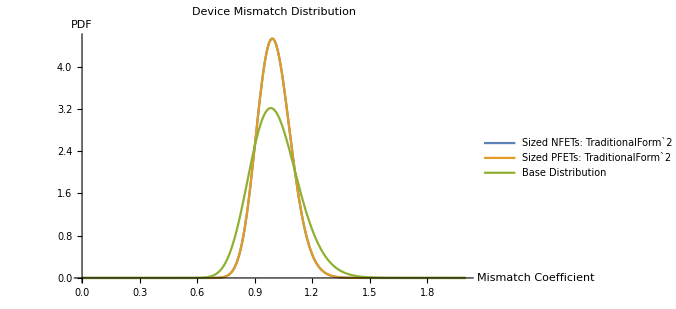
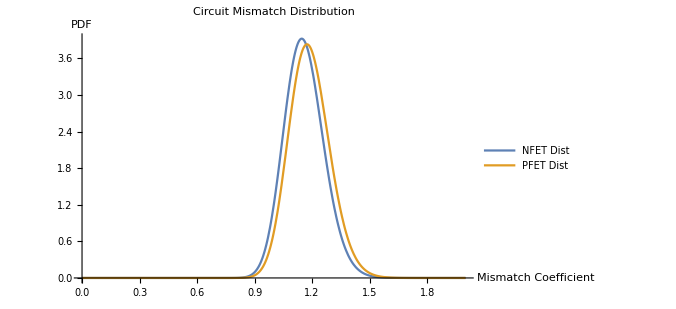
Area under NFET mismatch distribution: 0.99846 | 
Area under PFET mismatch distribution: 0.996435 | 
-Graphics- | -Graphics-

```mathematica
Block[{μn=0, σn=0.125, sizeMultN=2,sizeMultP=2,seedNum=21,imgSize=500,ℒ𝒩N, ℒ𝒩P, INDist,IPDist, Nj, Pj, B1, B2, B3,popCoverageN, popCoverageP,distPlot},
ℒ𝒩N=LogNormalDistribution[μn,σn/√sizeMultN];
ℒ𝒩P=LogNormalDistribution[μn,σn/√sizeMultP];
SeedRandom[seedNum];
B1=RandomVariate[ℒ𝒩N];
B2=RandomVariate[ℒ𝒩N];
B3=RandomVariate[ℒ𝒩P];
(*B1=RandomVariate[LogNormalDistribution[μn,σn]];
B2=RandomVariate[LogNormalDistribution[μn,σn]];
B3=RandomVariate[LogNormalDistribution[μn,σn]];*)
INDist=TransformedDistribution[Nj/B1,{Nj\[Distributed]ℒ𝒩N}];
IPDist=TransformedDistribution[(Pj B2)/(B1 B3),{Pj\[Distributed]ℒ𝒩P}];
popCoverageN=NIntegrate[PDF[INDist,x],{x,0.5,1.5},Method->"LocalAdaptive"];
popCoverageP=NIntegrate[PDF[IPDist,x],{x,0.5,1.5},Method->"LocalAdaptive"];
inputDistPlot=Plot[{PDF[ℒ𝒩N,x],PDF[ℒ𝒩P,x],PDF[LogNormalDistribution[μn,σn],x]},
{x,0,2},PlotRange->All,ImageSize->imgSize,PlotLabel->"Device Mismatch Distribution",
PlotLegends->Placed[{ StringForm["Sized NFETs: ``",sizeMultN],StringForm["Sized PFETs: ``",sizeMultP],"Base Distribution"},{Scaled[{0.75,0.8 }],{0.45,Center}}],
AxesLabel->{"Mismatch Coefficient", "PDF"}];
outputDistPlot=Plot[{PDF[INDist,x],PDF[IPDist,x]},
{x,0,2},PlotRange->All,ImageSize->imgSize,PlotLabel->"Circuit Mismatch Distribution",
PlotLegends->Placed[{"NFET Dist", "PFET Dist"},{Scaled[{0.75,0.8 }],{0.45,Center}}],
AxesLabel->{"Mismatch Coefficient", "PDF"}];

Grid[{
{StringForm["Area under NFET mismatch distribution: ``",popCoverageN]},
{StringForm["Area under PFET mismatch distribution: ``",popCoverageP]},
{inputDistPlot,outputDistPlot}
}, Alignment->Left]
]
```

The calculations below were quick experiments that I was running with Alex to better understand whether the law of large numbers might help me out.  It turns out that although it would appear to help, it doesn’t actually help us because we are still trying to optimize for speed of one inverter gate’s delay, rather than just optimizing for mismatch.

```mathematica
areaaboveTail=NIntegrate[PDF[LogNormalDistribution[0,0.125],x],{x,0,0.5},Method->"LocalAdaptive"]
areaaboveTail^2
NIntegrate[PDF[LogNormalDistribution[0,0.125/√2],x],{x,0,0.5},Method->"LocalAdaptive"]
```

1.46828×10^-8

2.15585×10^-16

2.21598×10^-15

```mathematica
areaaboveTail^3
NIntegrate[PDF[LogNormalDistribution[0,0.125/√3],x],{x,0,0.5},Method->"LocalAdaptive"]
```

3.16539×10^-24

4.27682×10^-22

## Appendix